{2,3,4,5,6,7,8,9,10,11}

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11}}

1.+1. x+9.67692×10^-17 x^2

{2.,3.,4.,5.,6.,7.,8.,9.,10.,11.}

5.32907×10^-15

9.30856×10^-30

2.84217×10^-15

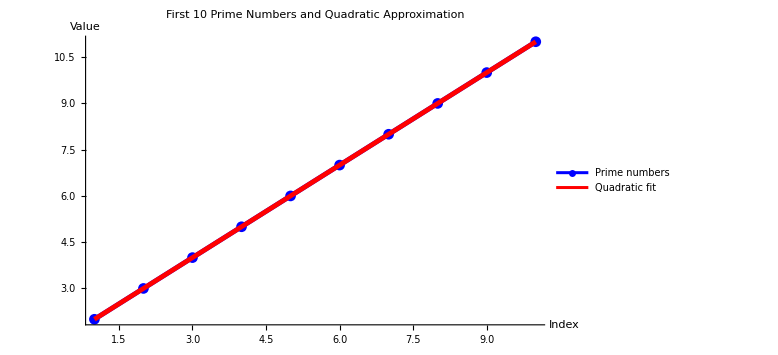

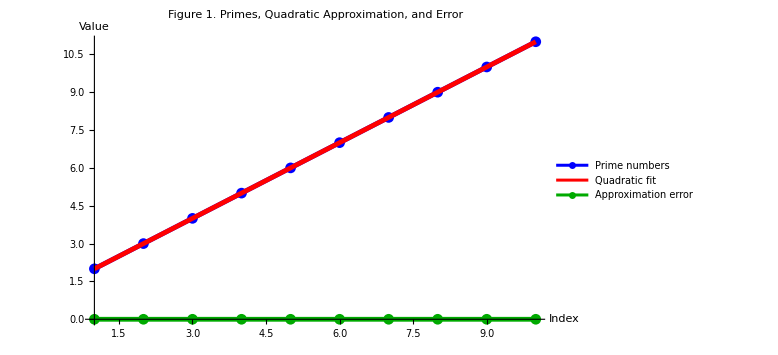

```mathematica
ClearAll["Global`*"];

primeList = {};
candidates = {};

Do[
  AppendTo[candidates, n];
  divisors = {};
  Do[
    If[IntegerQ[N[n/k]] && Mod[n, k] == 0, AppendTo[divisors, k]],
    {k, 2, n - 1}
  ];
  If[Complement[divisors, {}] === {} && n > 1, AppendTo[primeList, n]];
  If[Length[primeList] >= 10, Break[]],
  {n, 2, 100}
];

xValues = Range[Length[primeList]];
points = Transpose[{xValues, primeList}];

fitModel = Fit[points, {1, x, x^2}, x];
approxValues = Table[fitModel /. x -> i, {i, xValues}];
errors = primeList - approxValues;

maxError = Max[Abs[errors]];
mse = N[Mean[errors^2]];
mae = N[Mean[Abs[errors]]];

combinedPlot = Show[
  ListPlot[
    points,
    Joined -> True,
    PlotStyle -> Directive[Blue, Thickness[0.006]],
    PlotMarkers -> Automatic,
    PlotLegends -> {"Prime numbers"},
    PlotLabel -> "First 10 Prime Numbers and Quadratic Approximation",
    AxesLabel -> {"Index", "Value"},
    AxesOrigin -> {1, 0},
    ImageSize -> Large
  ],
  Plot[
    fitModel,
    {x, 1, Length[primeList]},
    PlotStyle -> Directive[Red, Thickness[0.006]],
    PlotLegends -> {"Quadratic fit"},
    AxesLabel -> {"Index", "Value"},
    AxesOrigin -> {1, 0},
    ImageSize -> Large
  ],
  PlotRange -> All,
  ImagePadding -> 20
];

figure1 = Show[
  combinedPlot,
  ListPlot[
    Transpose[{xValues, errors}],
    Joined -> True,
    PlotStyle -> Directive[Darker[Green], Thickness[0.006]],
    PlotMarkers -> Automatic,
    PlotLegends -> {"Approximation error"},
    AxesLabel -> {"Index", "Error"},
    AxesOrigin -> {1, 0},
    ImageSize -> Large
  ],
  PlotRange -> All,
  PlotLabel -> "Figure 1. Primes, Quadratic Approximation, and Error",
  ImagePadding -> 20
];

primeList
points
fitModel
approxValues
maxError
mse
mae
combinedPlot
figure1
```